```mathematica
data={{16,3340,3330},{18,3000,3000},{20,2810,2770},{22,2590,2530},{24,2380,2400},{26,2180,2160},{28,1990,1970},{30,1790,1770},{32,1650,1640},{34,1540,1520},{36,1360,1380},{38,1310,1300},{40,1210,1180},{42,1110,1090},{44,1020,990},{46,950,930},{48,860,880},{50,810,790},{52,740,740},{54,690,680},{56,630,630},{58,580,580},{60,560,550},{62,520,510},{64,470,480},{66,460,440},{68,420,420},{70,380,380},{72,360,360},{74,340,330}};
separated=Join[data[[All, {1, 2}]], data[[All, {1, 3}]]];

measurementsPlot=ListPlot[separated, AxesLabel->{"Temperatura (°C)", "Resistência Elétrica (Ω)"}];
Export[NotebookDirectory[]<>"Images/NTC-MeasurementsPlot.pdf", measurementsPlot];
fitted=NonlinearModelFit[separated, Subscript[R, 0] Exp[β(1/(T+273))], {Subscript[R, 0], β}, T];

fitPlot=Show[
ListPlot[separated,PlotStyle->Red],
Plot[fitted[T], {T, Min[separated[[All, 1]]], Max[separated[[All, 1]]]}],
AxesLabel->{"Temperatura (°C)", "Resistência Elétrica (Ω)"}
];
Export[NotebookDirectory[]<>"Images/NTC-FitPlot.pdf", fitPlot];
```

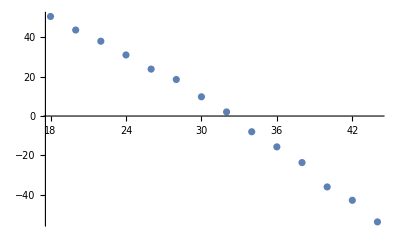

18 | 50.7
20 | 43.8
22 | 38.1
24 | 31.1
26 | 23.9
28 | 18.6
30 | 9.8
32 | 2.1
34 | -8
36 | -15.7
38 | -23.7
40 | -36.1
42 | -42.9
44 | -53.9

```mathematica
data={{18,50.7},{20,43.8},{22,38.1},{24,31.1},{26,23.9},{28,18.6},{30,9.8},{32,2.1},{34,-8},{36,-15.7},{38,-23.7},{40,-36.1},{42,-42.9},{44,-53.9}};

ListPlot[data]
Grid[data]

Export[NotebookFileName[EvaluationNotebook[]]<>".pdf", EvaluationNotebook[]];
```